```mathematica
(*** Here 2 versions of niche width is obtained ***)
MeanFieldCompet[input_,initial_]:=Module[{b,ns,nstep,T,a,ca,muR=0.1,qS,nu,step,Q,rho,initialE,initialO,systemE,systemO,fE,fO,Fitness,Fullsystem,variableE,variableO,Fullvariable,Solution,tempResult,Result,NBes},
ns=input[[1]];
b=input[[2]];
If[b==0,Result=ConstantArray[0,ns+2];Goto[end]];
nstep=input[[3]];
T=input[[4]];
nu=input[[5]];
ca= input[[6]];
step=1./nstep;

(***  here nu is defined differently  ***)
(*nu=If[ns≠0,w/(ns)^2];*)
(*nu=If[ns≠0,w/4^2];*)
Q=Range[0+step,1,step];
qS=If[ns==0,0.5,Range[1/ns,1,1/ns]];
a=Flatten[{ca 0.5,ConstantArray[0.5,ns]}];

(*NBes =BesselI[0,1/nu]; 
Fitness[q_,k_]:=If [k==1,1. ,Exp[1/nu*  Cos[2 Pi q- 2 Pi qS[[k-1]]]]/NBes];*)

NBes =Log@BesselI[0,1/nu]; 
Fitness[q_,k_]:=If [k==1,1. ,Exp[(1/nu*  Cos[2 Pi q- 2 Pi qS[[k-1]]])- NBes]];

If[Length@initial==0,
initialE= Table[rho[q,0][0]==0.1*b/muR,{q,Q}];
initialO= Table[rho[q,k][0]==1/(ns+1)*b/muR,{k,ns+1},{q,Q}] ,(*ns is the number of specialist so +1 adds the generalist*)
initialE= Table[rho[Q[[i]],0][0]==initial[[i,1]],{i,Length@Q}];
initialO= Table[rho[Q[[i]],k][0]==initial[[i,k+1]],{k,ns+1},{i,Length@Q}] 
];

fE[q_,t_]:= b- muR* rho[q,0][t]- rho[q,0][t]* Sum[a[[k]]*Fitness[q,k]* Sum[step*rho[qq,k][t],{qq,Q}],{k,ns+1}];
fO[q_,t_,k_]:=-muR *rho[q,k][t]+rho[q,0][t]* a[[k]]*Fitness[q,k]* Sum[step*rho[qq,k][t],{qq,Q}];

systemE=Table[rho[q,0]'[t]==fE[q,t],{q,Q}];
systemO=Table[rho[q,k]'[t]==fO[q,t,k],{k,ns+1},{q,Q}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[rho[q,0],{q,Q}];
variableO=Table[rho[q,k],{k,ns+1},{q,Q}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,T},Method->{"EquationSimplification"->"Residual"}];

tempResult=Flatten[Evaluate[Table[rho[q,k][T],{q,Q},{k,0,ns+1,1}] /.Solution],1];

Result=step*Total[tempResult];
Label[end];
{Result,tempResult}];
```

```mathematica
CompetModel[input_]:=Module[{b,nu,ca,init, difference,time,eps,peps,(*totalresult={},*)nstep=100,finalresult={},lastresult,newresult,diff,epscheck,tresult,rawresult,initial},
nu=input[[1]];
ca=input[[2]];
nstep = input[[3]];
peps = input[[4]];
b = input[[5]];(*2.;*)
eps = 10^(-peps);
Do[
time=10000;
lastresult=ConstantArray[0,ns+2];initial={};
difference=True;
While[difference==True,
init= {ns,b,nstep,time,nu,ca};
rawresult=Chop[MeanFieldCompet[init,initial]];
newresult=rawresult[[1]];
initial=rawresult[[2]];
tresult=Total[newresult];
(*AppendTo[totalresult,newresult];*)
diff=Abs[newresult-lastresult];
epscheck=Total[Boole[And[Table[diff[[k]]>eps,{k,ns+2}]]]];
If[epscheck==0,difference=False];
lastresult=newresult;
time+=10000;
If[time>10^7,Goto[leave]];
];
Label[leave];
AppendTo[finalresult,Flatten@{ns,newresult/tresult}];
,{ns,Flatten[{Range[10]}]}];
(*Export[StringJoin["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure2\\Panel a\\with_compet_w_" ,ToString[w],"_ca_",ToString[ca],"_nstep_",ToString@nstep, "_eps_",ToString@eps,"_b_",ToString@b,".csv"],finalresult];*)
Export[StringJoin["Z:\\fig2bc\\fig2bc_nu_" ,ToString[nu],"_ca_",ToString[ca],"_nstep_",ToString@nstep, "_peps_",ToString@peps,"_b_",ToString@b,".csv"],finalresult];
];
```

```mathematica
PARAM=Flatten[Table[{nu,ca,nstep,eps,b},{nu,{0.125,1.5}},{ca,{0.8}},{nstep,{100}},{eps,{7}},{b,{2}}],4]//N;
```

```mathematica
DistributeDefinitions[CompetModel,MeanFieldCompet,PARAM]
```

{CompetModel,MeanFieldCompet,PARAM}

```mathematica
tt=AbsoluteTiming[ParallelMap[CompetModel,PARAM]];
```

## Figure 2bc

```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure2\\";
```

```mathematica
(*Export data as dg and ds*)
DGS[dat_,b_,ca_]:= Module[{result,dg,ds1,ds,nospe,muR= 0.1, aa = 0.5},

dg = dat[[All,{1,3}]];
nospe = {0, 1- muR^2/ (b ca aa)};
AppendTo[dg,nospe];
ds1 =dg;
Do[
ds1[[ii]] = Mean[dat[[ii,4;;]]]; 
,{ii,Length[dat]}];
ds = {dg[[All,1]],ds1}//Transpose;
result = {dg,ds};
result]
```

### Figure 2b

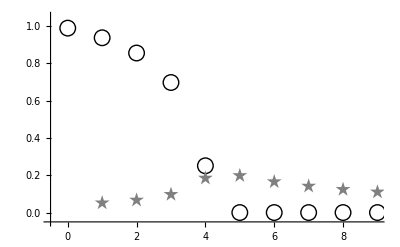

```mathematica
b= 2;
ca= 0.8;

ao ={-0.5,-0.05};

db = Import[localdir<>"Panel abc\\fig2bc_nu_0.125_ca_0.8_nstep_100._peps_7._b_2..csv"];
dbb=DGS[db,b,ca];
fig2b = ListPlot[dbb, PlotRange-> {{-0.5,9},{-0.05,1.05}},AxesOrigin->ao,PlotStyle-> {Black, Gray},PlotMarkers->pm,AxesStyle-> as2,PlotRangePadding->{{0,0.5},{0,0}},Ticks-> {Range[0,9,1],Automatic}]
```

```mathematica
Export[localdir<>"fig2b.jpeg",fig2b,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\fig2b.jpeg

### Figure 2c

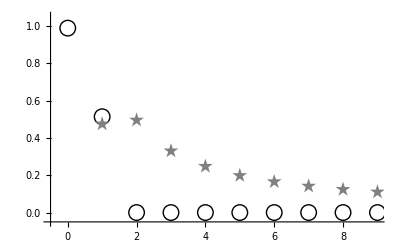

```mathematica
b= 2;
ca= 0.8;


dc = Import[localdir<>"Panel abc\\fig2bc_nu_1._ca_0.8_nstep_100._peps_7._b_2..csv"];
dcc=DGS[dc,b,ca];
fig2c = ListPlot[dcc, PlotRange-> {{-0.5,9},{-0.05,1.05}},AxesOrigin->ao,PlotStyle-> {Black, Gray},PlotMarkers->pm,AxesStyle-> as2,PlotRangePadding->{{0,0.5},{0,0}},Ticks-> {Range[0,9,1],Automatic}]
```

```mathematica
Export[localdir<>"fig2c.jpeg",fig2c,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure2\fig2c.jpeg